```mathematica
Fspring[s_]:=(b Em h^3 s)/(4 Ls^3)
```

```mathematica
Ls = 0.20;
h = 0.6*10^-3;
b=2.8*10^-2;
Em = 100*10^9;
M = (150.74*10^-3)/1.03*Ls; (*масса колебающегося конца линейки*)
m = 0; (*масса грузика на конце линейки, при m=0 грузика нет и есть только собственные колебания линейки*)
l=0.24; (*удаление грузика от оси вращения*)
```

```mathematica
Ioverall = (M Ls^2)/3+m l^2
```

0.000390265

```mathematica
solution = DSolve[{α''[t] == -Fspring[α[t] * Ls]/Ioverall, α[0] == 0.1, α'[0] ==0},α[t], t]
```

{{α[t]→0.1 Cos[98.416 t]}}

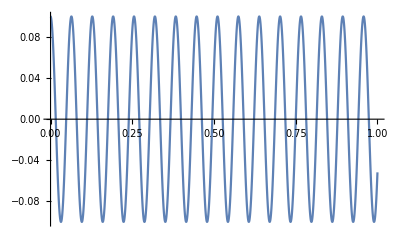

```mathematica
Plot[solution[[1, 1, 2]], {t, 0, 1}]
```

```mathematica
98.41604101380572/(2Pi)
```

15.6634

```mathematica
DSolve[{x''[t] == -(3E b h^3)/(4M Ls^3) x[t], x[0] == 1, x'[0] == 0}, x[t], t]
```

{{x[t]→1. Cos[0.000229471 t]}}